```mathematica
GravPotential[M_,m_,G_, sourceX_,sourceY_,testX_, testY_]:=-(G*M*m)/EuclideanDistance[{sourceX, sourceY}, {testX, testY}]
```

```mathematica
Plot3D[GravPotential[1, 1, 1, 0, 0, x, y], {x, -4, 4}, {y, -4, 4}]
```

-Graphics3D-

```mathematica
TwoGrav[M1_, M2_, X1_, X_, Y_]:=GravPotential[M1, 1, 0.00001, X1, 0, X, Y] + GravPotential[M2, 1, 0.00001, -M1/M2 X1, 0, X,  Y]
```

```mathematica
ContourPlot[TwoGrav[25,1, -25, x, y], {x, -750, 750}, {y, -750, 750}, ClippingStyle->Automatic, MaxRecursion->5, Contours->30]
Plot3D[TwoGrav[25,1, -25, x, y], {x, -750, 750}, {y, -750, 750}, PlotPoints->25, MaxRecursion->4]
```

-Graphics-

-Graphics3D-

```mathematica
Centrifugal[w_,m_,x_, y_]:= -1/2 w^2*m*EuclideanDistance[{0,0},{x,y}]
```

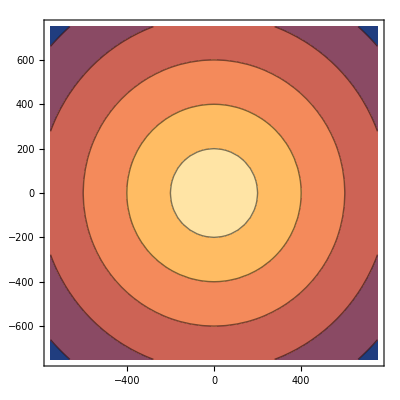

-Graphics3D-

```mathematica
ContourPlot[Centrifugal[1, 0.001, x, y],{x,-750,750},{y,-750,750}]
Plot3D[Centrifugal[1, 0.001, x, y],{x,-750,750},{y,-750,750}]
```

```mathematica
mass:=0.01
Manipulate[GraphicsColumn[{
GraphicsRow[{
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y],{x, -5, 5}, {y, -5, 5},PlotRange->{-7*10^-7,-3*10^-8}, Mesh->None, PlotLabel->"Gravitational Potential"],
Plot3D[Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5},PlotRange->{-1.5*10^-7,0}, Mesh->None, PlotLabel->"Centrifugal Potential"]
}],
GraphicsRow[{
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential"],
ContourPlot[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->2, Contours->20, PlotLabel->"Combined Effective Potential"]
}]
}],
{spin,0,0.07},{separation,0,3},{ratio,1,3}]
```

```mathematica
mass:=0.01
separation:=0
ratio:=1
Export["spin.gif",Table[
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]],
{spin,0,0.07,0.003}]]
```

spin.gif

```mathematica
mass:=0.01
spin:=0.066
ratio:=1
Export["separation.gif",Table[GraphicsRow[{
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]],
ContourPlot[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30,Contours->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]]}],
{separation,0,1.5, 0.02}]]
```

separation.gif

```mathematica
mass:=0.01
spin:=0.066
separation:=1.5
Export["ratio.gif",Table[GraphicsRow[{
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]],
ContourPlot[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30,Contours->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]]}],
{ratio,1,5,0.1}]]
```

ratio.gif